{P_(1,1)→PG11,P_(1,2)→PG12,P_(1,3)→PG13,P_(2,2)→PG22,P_(2,1)→PG21,P_(3,1)→PG31,P_(2,3)→PG23,P_(3,2)→PG32,P_(3,3)→PG33,P_1→P1,P_2→P2,P_3→P3,u_1→u1,u_2→u2,u_3→u3,u_4→u4,u_5→u5,u_6→u6}

3.872×10^11 Pz^7+6 Pz^5 (1.39×10^10-3.2×10^7 T)+722000. Pz (-391+T)+4 Pz^3 (-1.83×10^9+4000000 T)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

3.872×10^11 Pz^7+6 Pz^5 (1.39×10^10-3.2×10^7 T)+722000. Pz (-391+T)+4 Pz^3 (-1.38841×10^9+4000000 T)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pz→ConditionalExpression[0,391.<T<400.||T<391.]},{Pz→ConditionalExpression[Root[-7.80533×10^19+1.99625×10^17 T+(-1.53551×10^21+4.42382×10^18 T) #1^2+(2.30591×10^22-5.30858×10^19 T) #1^4+1.07056×10^23 #1^6&,2],T<391.]}}

Root[-7.80533×10^19+1.99625×10^17 T+(-1.53551×10^21+4.42382×10^18 T) #1^2+(2.30591×10^22-5.30858×10^19 T) #1^4+1.07056×10^23 #1^6&,2]

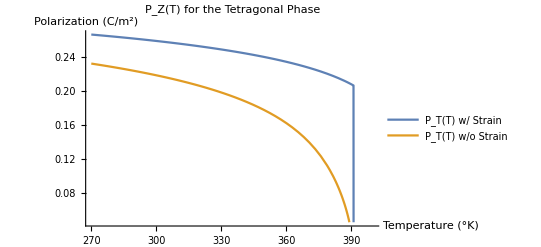

```mathematica
FPolar[P_]=Subscript[a,1](Sum[Subscript[P,i]^2, {i,1,3}])  +Subscript[a,11](Sum[Subscript[P,i]^4,{i,1,3}])+Subscript[a,12](Sum[Subscript[P,i]^2*Subscript[P,j]^2, {j,1,3}, {i,1,j-1}]) +
Subscript[a,111](Sum[Subscript[P,i]^6, {i,1,3}])+1/2*Simplify[Subscript[a,112](Sum[Subscript[P,i]^2*(Subscript[P,j]^4+Subscript[P,k]^4)(Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3} ,{j,1,3}, {k,1,3}])]+Subscript[a,123](Sum[Subscript[P,i]^2Subscript[P,j]^2Subscript[P,k]^2, {i,1,3},{j,1,i-1},{k,1,j-1}])/.{False->0, True->1};
ThermodynamicCoefficients={ a1->3.61*10^5*(T-391),a11->-1.83*10^9+4*10^6*T,a12->-2.24*10^9+6.7*10^6*T,
a111->1.39*10^10-3.2*10^7*T,a112->-2.2*10^9,a123->5.51*10^10,
a1111->4.84*10^10,a1112->2.53*10^11,a1122->2.80*10^11,a1123->9.35*10^10, 
q11->14.20*10^9,q12->-0.74*10^9,q44->1.57*10^9};

CoefficientsToVariables={Subscript[a, 1]->a1,Subscript[a, 11]->a11, Subscript[a, 12]->a12,Subscript[a, 111]->a111,Subscript[a, 112]->a112,Subscript[a, 123]->a123,
Subscript[a, 1111]->a1111,Subscript[a, 1112]->a1112,Subscript[a, 1122]->a1122,Subscript[a, 1123]->a1123,
Subscript[c, 11]->c11,Subscript[c, 12]->c12,Subscript[c, 44]->c44,Subscript[q, 11]->q11,Subscript[q, 12]->q12,Subscript[q, 44]->q44};
TElasticConstants={c11-> 300*10^9,c12->109*10^9};
OElasticConstants={c11->150*10^9,c22->312*10^9,c33->150*10^9,c44->135*10^9,c12->100*10^9};
Renormalization={A11->Subscript[a, 11]+1/2*((c11 q11+c12 q11-2 c12 q12) Subscript[q, 11])/(c11^2+c11 c12-2 c12^2)+((-c12 q11+c11 q12) Subscript[q, 12])/((c11-c12) (c11+2 c12))};

(*
PhiPz=D[FPolar[P]/.SubToVariableRules, P3]/.P1->0/.P2->0;
Solve[PhiPz==0, P3];
PhiPzRenormalized[Pz_]=2 a1 Pz+4 A11 Pz^3 +6 a111 Pz^5 ;
Solve[PhiPzRenormalized[Pz]==0, Pz];
*)

(* Non-Elastic Subsystem T-Polarization *)
PhiPzTetragonal[Pz_]=2 a1 Pz+4 a11 Pz^3 +6 a111 Pz^5 +8 a1111 Pz^7/.ThermodynamicCoefficients
Solve[(PhiPzTetragonal[Pz]==0)&& T<391 && Pz≥0, Pz, Reals];
TetragonalRoot=Simplify[Pz/.Normal[%][[2]]];
Plot[TetragonalRoot, {T, 270,400}];
FindMinimum;
(* Elastic Subsystem T-Polarization *)
PhiPzTetragonalElastic[Pz_]=(2 a1 Pz+4 A11 Pz^3+6 a111 Pz^5 +8 a1111 Pz^7/.Renormalization)/.CoefficientsToVariables/.ThermodynamicCoefficients/.TElasticConstants
Solve[(PhiPzTetragonalElastic[Pz]==0)&& T<400 && Pz≥0, Pz, Reals]
TetragonalElasticRoot=Simplify[Pz/.Normal[%][[2]]]
Plot[{TetragonalRoot, TetragonalElasticRoot}, {T, 270,400}, PlotLegends->{"P_T(T) w/ Strain", "P_T(T) w/o Strain"}, AxesLabel->{"Temperature (°K)", "Polarization (C/m^2)"}, PlotLabel->"P_Z(T) for the Tetragonal Phase" ]
```

√2 a1 P+((2 a11+a12) P^3)/(√2)+(3 (a111+a112) P^5)/(2 √2)+((2 a1111+2 a1112+a1122) P^7)/(2 √2)

{{P→ConditionalExpression[0,1]},{P→ConditionalExpression[Root[4 a1+(4 a11+2 a12) #1^2+(3 a111+3 a112) #1^4+(2 a1111+2 a1112+a1122) #1^6&,2],1]},{P→ConditionalExpression[Root[4 a1+(4 a11+2 a12) #1^2+(3 a111+3 a112) #1^4+(2 a1111+2 a1112+a1122) #1^6&,3],1]},{P→ConditionalExpression[Root[4 a1+(1) #1^2+1+(2 a1111+2 a1112+a1122) #1^6&,4],1]},{P→ConditionalExpression[Root[4 a1+(4 a11+2 a12) #1^2+(3 a111+3 a112) #1^4+(2 a1111+2 a1112+a1122) #1^6&,5],1]},{P→ConditionalExpression[Root[4 a1+(4 a11+2 a12) #1^2+(3 a111+3 a112) #1^4+(2 a1111+2 a1112+a1122) #1^6&,6],1]}}
 |  |  |  |

Root[4 a1+(4 a11+2 a12) #1^2+(3 a111+3 a112) #1^4+(2 a1111+2 a1112+a1122) #1^6&,2]

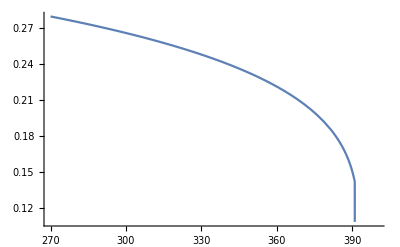

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Orthorhombic Phase

```mathematica
(*_________________________________________________________________________________________________________________________________________________________*)

(*Orthorhombic Numerical Evaluation Cell *)

(* Non-Elastic Subsystem O-Polarization *)
PhiPOrthorhombic[P_]=Collect[Sqrt[2]*a1*P + Sqrt[2]*a11*P^3 + (a12*P^3)/Sqrt[2] + (3*a111*P^5)/(2*Sqrt[2]) + (3*a112*P^5)/(2*Sqrt[2]) + (a1111*P^7)/Sqrt[2] + (a1112*P^7)/Sqrt[2] + (a1122*P^7)/(2*Sqrt[2]),P,Simplify]
Solve[(PhiPOrthorhombic[P]==0)&& T<391 && P≥0, P, Reals]
OrthorhombicRoot=Simplify[P/.Normal[%][[2]]]
Plot[OrthorhombicRoot/.ThermodynamicCoefficients, {T, 270,400}]

(* Elastic Subsystem O-Polarization *)
PhiPOrthorhombicElastic[P_]=Sqrt[2]*a1*P + Sqrt[2]*A11*P^3 + (A12*P^3)/Sqrt[2] + (3*a111*P^5)/(2*Sqrt[2]) + (3*a112*P^5)/(2*Sqrt[2]) + (a1111*P^7)/Sqrt[2] + (a1112*P^7)/Sqrt[2] + (a1122*P^7)/(2*Sqrt[2])/.ThermodynamicCoefficients//.CoefficientsToVariables/.ThermodynamicCoefficients/.OElasticConstants;
Solve[(PhiPOrthorhombicElastic[P]==0)&& T<391 && P≥0, P, Reals];
OrthorhombicElasticRoot=Simplify[P/.Normal[%][[2]]];
Plot[{OrthorhombicRoot,OrthorhombicElasticRoot}, {T, 150,392}, PlotLegends->{"P_O(T) w/o Strain", "P_O(T) w/ Strain"}, AxesLabel->{"Temperature (°K)", "Polarization (C/m^2)"}, PlotLabel->"P(T) for the Orthorhombic Phase" ];
Orthorhombic Phase
```

{a_12 P_1^2 P_3^2+a_1 (P_1^2+P_3^2)+a_112 P_1^2 P_3^2 (P_1^2+P_3^2)+a_11 (P_1^4+P_3^4)+a_111 (P_1^6+P_3^6)}

-1.83×10^9+4000000 T→1.56507×10^9

-2.24×10^9+6.7×10^6 T→-1.3248×10^9

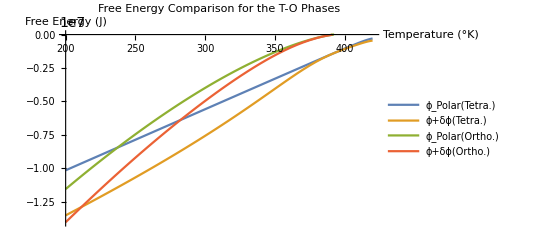

```mathematica
(*___________________________________________________________________________________________________________________________________________________________________________________*)
(* Inserting the polarization solutions into the free energy for each respective phase determines the most stable phase (i.e. the phase with the lowest free energy) *)

(* For the Tetragonal Phase *)
FTetragonalPolar=Simplify[(FPolar[P])/.SubToVariableRules]/.{P1->0,P2->0,P3->P0}/.VariableToSubRules;
δϕ=(FBulk[P,u]-FPolar[P])/.SubToVariableRules/.StrainSolutions/.P2->0/.P1->0/.P3->P0;
FTetragonalPolarEvaluated=FTetragonalPolar/.P0-> √((-a11+√(a11^2-3 Subscript[a, 1] Subscript[a, 111]))/(3 Subscript[a, 111]))/.CoefficientsToVariables/.ThermodynamicCoefficients;
δϕTEvaluated=δϕ/.P0-> √((-a11+√(a11^2-3 Subscript[a, 1] Subscript[a, 111]))/(3 Subscript[a, 111]))/.CoefficientsToVariables/.(a11->Subscript[a, 11]+1/2*((c11 q11+c12 q11-2 c12 q12) Subscript[q, 11])/(c11^2+c11 c12-2 c12^2)+((-c12 q11+c11 q12) Subscript[q, 12])/((c11-c12) (c11+2 c12)))/.CoefficientsToVariables/.ThermodynamicCoefficients/.TElasticConstants;
Plot[{FTetragonalPolarEvaluated, FTetragonalPolarEvaluated+δϕTEvaluated}, {T, 200,420},  PlotLegends->{"ϕ_Polar(T)", "ϕ_Polar-δϕ"}, AxesLabel->{"Temperature (°K)", "Free Energy (J)"}, PlotLabel->"Free Energy Comparison for the Tetragonal Phase" ];

(* For the Orthorhombic Phase *)
P=.
Collect[Simplify[(FPolar[P])/.SubToVariableRules/.StrainSolutions/.P2->0]/.VariableToSubRules, {Subscript[a, 1],Subscript[a, 11],Subscript[a, 111]}]
FOrthorhombic=Simplify[(FPolar[P])/.SubToVariableRules]/.StrainSolutions/.P1->OrthorhombicRoot/2^(1/2)/.P2->0/.P3->OrthorhombicRoot/2^(1/2)/.Q44->(q44/c44)//.CoefficientsToVariables/.ThermodynamicCoefficients/.OElasticConstants;
δϕOEvaluated=(FBulk[P,u]-FPolar[P])/.SubToVariableRules/.StrainSolutions/.P2->0/.P1->P3//.P3-> OrthorhombicRoot/2^(1/2)/.CoefficientsToVariables/.(a11->Subscript[a, 11]+1/2*((c11 q11+c12 q11-2 c12 q12) Subscript[q, 11])/(c11^2+c11 c12-2 c12^2)+((-c12 q11+c11 q12) Subscript[q, 12])/((c11-c12) (c11+2 c12)))/.( a12->Subscript[a, 12]+((-c12 q11+c11 q12) Subscript[q, 11])/((c11-c12) (c11+2 c12))+((-c12 q11+c11 q12) Subscript[q, 12])/((c11-c12) (c11+2 c12))+((c11 q11+c12 q11-2 c12 q12) Subscript[q, 12])/(c11^2+c11 c12-2 c12^2)+Q44 Subscript[q, 44]/2)/.Q44->q44/c44/.CoefficientsToVariables/.ThermodynamicCoefficients/.OElasticConstants;
(a11->1/2*((c11 q11+c12 q11-2 c12 q12) Subscript[q, 11])/(c11^2+c11 c12-2 c12^2)+((-c12 q11+c11 q12) Subscript[q, 12])/((c11-c12) (c11+2 c12)))/.Q44->q44/c44/.CoefficientsToVariables/.ThermodynamicCoefficients/.OElasticConstants
( a12->((-c12 q11+c11 q12) Subscript[q, 11])/((c11-c12) (c11+2 c12))+((-c12 q11+c11 q12) Subscript[q, 12])/((c11-c12) (c11+2 c12))+((c11 q11+c12 q11-2 c12 q12) Subscript[q, 12])/(c11^2+c11 c12-2 c12^2)+Q44 Subscript[q, 44]/2)/.Q44->q44/c44/.CoefficientsToVariables/.ThermodynamicCoefficients/.OElasticConstants

Plot[{FOrthorhombic,FOrthorhombic-δϕOEvaluated}, {T,150,360}];
Plot[{FTetragonalPolarEvaluated, FTetragonalPolarEvaluated+δϕTEvaluated,FOrthorhombic,FOrthorhombic+δϕOEvaluated}, {T, 200,420},  PlotLegends->{"ϕ_Polar(Tetra.)","ϕ+δϕ(Tetra.)", "ϕ_Polar(Ortho.)","ϕ+δϕ(Ortho.)"}, AxesLabel->{"Temperature (°K)", "Free Energy (J)"}, PlotLabel->"Free Energy Comparison for the T-O Phases" ]


(* For the Monoclinic Phase *)
FMonoclinic=Simplify[(FBulkRenormalized[P]-FGradient[P])/.SubToVariableRules]/.
{P1->P1Monoclinic,P2->0,P3->P3Monoclinic}/.VariableToSubRules;
(*FinalFreeEnergies={Simplify[(FTetragonal//.CoefficientsToVariables/.ThermodynamicCoefficients)],
Simplify[(FOrthorhombic//.CoefficientsToVariables/.ThermodynamicCoefficients)],
Simplify[(FMonoclinic//.CoefficientsToVariables/.ThermodynamicCoefficients)]};
Plot[{0*T,FinalFreeEnergies[[1]],FinalFreeEnergies[[2]],FinalFreeEnergies[[3]]} ,{T, 0,400}, PlotLegends->{"Cubic Free Energy","Tetragonal Free Energy","Orthorhombic Free Energy","Monoclinic Free Energy" }, AxesLabel->{"Temperature (°K)", "Free Energy"}, PlotLabel->"Free Energy for the T,O, and Mc Phases"]*)
```

```mathematica
(*_________________________________________________________________________________________________________________________________________________________*)

(*Monoclinic Numerical Evaluation Cell *)

(* Elastic Subsystem Mc-Polarization *)
PhiP1Monoclinic[P1_,P3_]=6 P1^5 Subscript[a, 111]+4 P1^3 (A11+P3^2 Subscript[a, 112])+2 P1 (A12 P3^2+Subscript[a, 1]+P3^4 Subscript[a, 112])//.CoefficientsToVariables/.ThermodynamicCoefficients/.OElasticConstants;
PhiP3Monoclinic[P1_,P3_]=6 P3^5 Subscript[a, 111]+2 P3^3 (2 A11+2 P1^2 Subscript[a, 112])+2 P3 (A12 P1^2+Subscript[a, 1]+P1^4 Subscript[a, 112])//.CoefficientsToVariables/.ThermodynamicCoefficients/.OElasticConstants;
MonoclinicSolutions=Solve[(PhiP1Monoclinic[P1,P3]==0)&&(PhiP3Monoclinic[P1,P3]==0)&& T<391 && P1≥ 0&&P3≥  0&&P1≠P3, {P1,P3}, Reals];
MonoclinicRootOne={Simplify[P1/.Normal[MonoclinicSolutions][[1,1]]], Simplify[P3/.Normal[MonoclinicSolutions][[1,2]]]};
MonoclinicRootTwo={Simplify[P1/.Normal[MonoclinicSolutions][[2,1]]], Simplify[P3/.Normal[MonoclinicSolutions][[2,2]]]};
MonoclinicRootThree={Simplify[P1/.Normal[MonoclinicSolutions][[3,1]]], Simplify[P3/.Normal[MonoclinicSolutions][[3,2]]]};
MonoclinicRootFour={Simplify[P1/.Normal[MonoclinicSolutions][[4,1]]], Simplify[P3/.Normal[MonoclinicSolutions][[4,2]]]};
MonoclinicRootFive={Simplify[P1/.Normal[MonoclinicSolutions][[5,1]]], Simplify[P3/.Normal[MonoclinicSolutions][[5,2]]]};

Plot[MonoclinicRootOne, {T, 150,392}, PlotLegends->{"P1(T)", "P3(T)"}, AxesLabel->{"Temperature (°K)", "Polarization (C/m^2)"}, PlotLabel->"P(T) for the Monoclinic Phase" ];
Plot[MonoclinicRootTwo, {T, 150,392}, PlotLegends->{"P1(T)", "P3(T)"}, AxesLabel->{"Temperature (°K)", "Polarization (C/m^2)"}, PlotLabel->"P(T) for the Monoclinic Phase" ];
Plot[MonoclinicRootThree, {T, 150,392}, PlotLegends->{"P1(T)", "P3(T)"}, AxesLabel->{"Temperature (°K)", "Polarization (C/m^2)"}, PlotLabel->"P(T) for the Monoclinic Phase"];
Plot[MonoclinicRootFour, {T, 150,392}, PlotLegends->{"P1(T)", "P3(T)"}, AxesLabel->{"Temperature (°K)", "Polarization (C/m^2)"}, PlotLabel->"P(T) for the Monoclinic Phase" ];
Plot[MonoclinicRootFive, {T, 150,392}, PlotLegends->{"P1(T)", "P3(T)"}, AxesLabel->{"Temperature (°K)", "Polarization (C/m^2)"}, PlotLabel->"P(T) for the Monoclinic Phase" ];
```

$Aborted

Part::partd: Part specification MonoclinicSolutions ⟦ 1, 1 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 1, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification MonoclinicSolutions ⟦ 1, 2 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 1, 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification MonoclinicSolutions ⟦ 2, 1 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 2, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification MonoclinicSolutions ⟦ 2, 2 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 2, 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification MonoclinicSolutions ⟦ 3, 1 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 3, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification MonoclinicSolutions ⟦ 3, 2 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 3, 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification MonoclinicSolutions ⟦ 4, 1 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 4, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification MonoclinicSolutions ⟦ 4, 2 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 4, 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification MonoclinicSolutions ⟦ 5, 1 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 5, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification MonoclinicSolutions ⟦ 5, 2 ⟧ is longer than depth of object.

ReplaceAll::reps: {MonoclinicSolutions ⟦ 5, 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*___________________________________________________________________________________________________________________________________________________________________________________*)
(*
(* Inserting the polarization solutions into the free energy for each respective phase determines the most stable phase (i.e. the phase with the lowest free energy) *)
FBulk=Subscript[a, 123] Subscript[P, 1]^2 Subscript[P, 2]^2 Subscript[P, 3]^2 + Subscript[a, 1] (Subscript[P, 1]^2+Subscript[P, 2]^2+Subscript[P, 3]^2) + Subscript[a, 12] (Subscript[P, 1]^2 Subscript[P, 2]^2 + Subscript[P, 1]^2 Subscript[P, 3]^2 + Subscript[P, 2]^2 Subscript[P, 3]^2) + Subscript[a, 11] (Subscript[P, 1]^4+Subscript[P, 2]^4+Subscript[P, 3]^4) + Subscript[a, 111] (Subscript[P, 1]^6+Subscript[P, 2]^6+Subscript[P, 3]^6) + Subscript[a, 112] (Subscript[P, 1]^4 (Subscript[P, 2]^2+Subscript[P, 3]^2) + Subscript[P, 2]^2 Subscript[P, 3]^2 (Subscript[P, 2]^2+Subscript[P, 3]^2) + Subscript[P, 1]^2 (Subscript[P, 2]^4+Subscript[P, 3]^4)) - Subscript[q, 11] (Subscript[P, 1]^2 Subscript[u, 1] + Subscript[P, 2]^2 Subscript[u, 2] + Subscript[P, 3]^2 Subscript[u, 3]) +  Subscript[c,  12] (Subscript[u, 1] Subscript[u, 2] + Subscript[u, 1] Subscript[u, 3] + Subscript[u, 2] Subscript[u, 3]) + 1/2 Subscript[c, 11] (Subscript[u, 1]^2+Subscript[u, 2]^2+Subscript[u, 3]^2) - Subscript[q, 12] (Subscript[P, 3]^2 (Subscript[u, 1]+Subscript[u, 2]) + Subscript[P, 2]^2 (Subscript[u, 1]+Subscript[u, 3]) + Subscript[P, 1]^2 (Subscript[u, 2]+Subscript[u, 3])) - Subscript[q,44] (Subscript[P, 2] Subscript[P, 3] Subscript[u, 4] + Subscript[P, 1] Subscript[P, 3] Subscript[u, 5] + Subscript[P, 1] Subscript[P, 2] Subscript[u, 6]) + 1/2 Subscript[c, 44] (Subscript[u, 4]^2+Subscript[u, 5]^2+Subscript[u, 6]^2);
(* For the Tetragonal Phase *)
FTetragonal=Simplify[FBulk/.SubToVariableRules/.P1->0/.P2->0];
FTetragonal=Simplify[FBulk/.SubToVariableRules//.P1->0//.P2->0/.u5-> 0/.StrainSolutions//.CoefficientsToVariables/.ThermodynamicCoefficients/.TElasticConstants/.P3->Pz/.Pz-> TetragonalElasticRoot/.P1->0]
Plot[{0*T,FTetragonal},{T,200,400}]
(* For the Orthorhombic Phase *)
FOrthorhombic;
(* For the Monoclinic Phase *)
FMonoclinic;
(*
FinalFreeEnergies={Simplify[(FTetragonal//.CoefficientsToVariables/.ThermodynamicCoefficients)],
Simplify[(FOrthorhombic//.CoefficientsToVariables/.ThermodynamicCoefficients)],
- Simplify[(FMonoclinic//.CoefficientsToVariables/.ThermodynamicCoefficients)]}; *)
(* Plot[{0*T,FinalFreeEnergies[[1]],FinalFreeEnergies[[2]],FinalFreeEnergies[[3]]} ,{T, 0,400}, PlotLegends->{"Cubic Free Energy","Tetragonal Free Energy","Orthorhombic Free Energy","Monoclinic Free Energy" }, AxesLabel->{"Temperature (°K)", "Free Energy"}, PlotLabel->"Free Energy for the T,O, and Mc Phases"]  *)
*)
```

```mathematica
(* Renormalization of Elastic Subsystem Coefficients *)

FStrainDerivative[P_,u_]={Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u1]], u1]/.VariableToSubRules,
Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u2]], u2]/.VariableToSubRules,Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u3]], u3]/.VariableToSubRules,
Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u4]], u4]/.VariableToSubRules, Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u5]], u5]/.VariableToSubRules,Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u6]], u6]/.VariableToSubRules}
ElectrostrictiveCoefficients={(-c12 q11+2 c11 q12)/(c11^2+c11 c12-2 c12^2)-> Q12, (c11 q11+c12 q11-4 c12 q12)/(c11^2+c11 c12-2 c12^2)-> Q11, q44/c44-> Q44}
StrainSolutions=Collect[Solve[{(FStrainDerivative[P,u][[1]]/.SubToVariableRules)==0,FStrainDerivative[P,u][[2]]==0/.SubToVariableRules,
FStrainDerivative[P,u][[3]]==0/.SubToVariableRules,FStrainDerivative[P,u][[4]]==0/.SubToVariableRules,FStrainDerivative[P,u][[5]]==0/.SubToVariableRules,FStrainDerivative[P,u][[6]]==0/.SubToVariableRules },{u1,u2,u3, u4,u5,u6}], {P1,P2,P3},Simplify]

Collect[StrainSolutions[[1,1]], {P1, P2, P3}]/.ElectrostrictiveCoefficients;

FStrainDerivative[P_,u_]={Collect[D[FBulk[P,u]/.SubToVariableRules, u1], u1, Simplify],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u2]], u2],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u3]], u3],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u4]], u4], Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u5]], u5],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u6]], u6]}/.CoefficientsToVariables
StrainSolutions=Collect[Solve[{(FStrainDerivative[P,u][[1]])==0,FStrainDerivative[P,u][[2]]==0,FStrainDerivative[P,u][[3]]==0,
FStrainDerivative[P,u][[4]]==0,FStrainDerivative[P,u][[5]]==0,FStrainDerivative[P,u][[6]]==0},{u1,u2,u3, u4,u5,u6}], {P1,P2,P3},Simplify][[1]]/.ElectrostrictiveCoefficients
```

ReplaceAll::reps: {SubToVariableRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {VariableToSubRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SubToVariableRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{0/.VariableToSubRules,0/.VariableToSubRules,0/.VariableToSubRules,0/.VariableToSubRules,0/.VariableToSubRules,0/.VariableToSubRules}

{(-c12 q11+2 c11 q12)/(c11^2+c11 c12-2 c12^2)→Q12,(c11 q11+c12 q11-4 c12 q12)/(c11^2+c11 c12-2 c12^2)→Q11,q44/c44→Q44}

ReplaceAll::reps: {SubToVariableRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Solve::naqs: (0/. VariableToSubRules/. SubToVariableRules) == 0 && ((0/. VariableToSubRules) == 0/. SubToVariableRules) && ((0/. VariableToSubRules) == 0/. SubToVariableRules) && ((0/. VariableToSubRules) == 0/. SubToVariableRules) && ((0/. VariableToSubRules) == 0/. SubToVariableRules) && ((0/. VariableToSubRules) == 0/. SubToVariableRules) is not a quantified system of equations and inequalities.

Solve[{(0/.VariableToSubRules/.SubToVariableRules)==0,(0/.VariableToSubRules)==0/.SubToVariableRules,(0/.VariableToSubRules)==0/.SubToVariableRules,(0/.VariableToSubRules)==0/.SubToVariableRules,(0/.VariableToSubRules)==0/.SubToVariableRules,(0/.VariableToSubRules)==0/.SubToVariableRules},{u1,u2,u3,u4,u5,u6}]

ReplaceAll::reps: {SubToVariableRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{0,0,0,0,0,0}

{}